```mathematica
Wolfram Project Summer School 2019
Subexpression identification algorithm for
very large symbolic expressions
```

## Rafael Guillermo González Acuña

When the symbolic expressions are very large, they are incomprehensible  to most human beings.

In this work, we present an algorithm that identifies common subexpressions and replaces them with characteristic variables such that is easier to grasp the overall structure of the original expression as well as providing insight into the components of the subexpressions.

First thing that we need to do is replace the Head of the expression in by List.

```mathematica
listifyHeads[exprs_List]:=Flatten[ReplacePart[#,0->List]&/@exprs]
```

```mathematica
listifyHeads[{1+x^2-3y}]
```

{1,x^2,-3 y}

Then the next step is to recursively apply this process to all levels of the expression. This is done in the function SubExpression.

The function SubExpression gives a list of the expression with common subexpressions replaced, the replacement rules, and subexpression rules.

```mathematica
SubExpression::usage="SubExpression[expr, depth, count] gives a list of the expression with common subexpression replace, the replacement rules, and subexpression rules, where depth is the level of complexity of the subexpression and count is the number of that subexpression repeats in the expression.";
SubExpression[expr_,depth_,count_]:=Module[{subexprs,replacerules},subexprs=DeleteDuplicates[Select[Flatten[FixedPointList[listifyHeads,{expr}]],Depth[#]>depth&&Count[expr,#,Infinity]≥count&&Head[#]=!=Power&]];
replacerules=(#->Framed[Subscript[α,Flatten[Position[subexprs-(#),0]][[1]]]])&/@subexprs;
{expr//.replacerules,replacerules,Reverse/@((#[[1]]//.DeleteCases[replacerules,#])->#[[2]]&/@replacerules)}
];
```

The following expression is an example,

```mathematica
expr1=(-ra ((ra (ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2))))/(n √(-ra^2+Ra^2) (1+ra^2/(-ra^2+Ra^2)) √(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))+(√(1-((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))^2)/(n^2 (1+ra^2/(-ra^2+Ra^2)) (ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))))/(√(1+ra^2/(-ra^2+Ra^2)))) ((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))/(n (1+ra^2/(-ra^2+Ra^2)) √(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))-(ra √(1-((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))^2)/(n^2 (1+ra^2/(-ra^2+Ra^2)) (ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))))/(√(-ra^2+Ra^2) √(1+ra^2/(-ra^2+Ra^2))))+(Ra-√(-ra^2+Ra^2)) ((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))/(n (1+ra^2/(-ra^2+Ra^2)) √(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))-(ra √(1-((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))^2)/(n^2 (1+ra^2/(-ra^2+Ra^2)) (ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))))/(√(-ra^2+Ra^2) √(1+ra^2/(-ra^2+Ra^2))))^2-n^2 (Ra-√(-ra^2+Ra^2)+t ((ra (ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2))))/(n √(-ra^2+Ra^2) (1+ra^2/(-ra^2+Ra^2)) √(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))+(√(1-((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))^2)/(n^2 (1+ra^2/(-ra^2+Ra^2)) (ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))))/(√(1+ra^2/(-ra^2+Ra^2)))))+((ra (ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2))))/(n √(-ra^2+Ra^2) (1+ra^2/(-ra^2+Ra^2)) √(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))+(√(1-((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))^2)/(n^2 (1+ra^2/(-ra^2+Ra^2)) (ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))))/(√(1+ra^2/(-ra^2+Ra^2))))^2 (t+tb)+n ((ra (ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2))))/(n √(-ra^2+Ra^2) (1+ra^2/(-ra^2+Ra^2)) √(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))+(√(1-((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))^2)/(n^2 (1+ra^2/(-ra^2+Ra^2)) (ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))))/(√(1+ra^2/(-ra^2+Ra^2)))) (ta-tb-√(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2) Sign[ta])+s1 √(((ra (ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2))))/(n √(-ra^2+Ra^2) (1+ra^2/(-ra^2+Ra^2)) √(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))+(√(1-((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))^2)/(n^2 (1+ra^2/(-ra^2+Ra^2)) (ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))))/(√(1+ra^2/(-ra^2+Ra^2))))^2 (n^2 (ra^2+2 ra t ((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))/(n (1+ra^2/(-ra^2+Ra^2)) √(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))-(ra √(1-((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))^2)/(n^2 (1+ra^2/(-ra^2+Ra^2)) (ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))))/(√(-ra^2+Ra^2) √(1+ra^2/(-ra^2+Ra^2))))+t^2 ((-1+(ra (ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2))))/(n √(-ra^2+Ra^2) (1+ra^2/(-ra^2+Ra^2)) √(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))+(√(1-((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))^2)/(n^2 (1+ra^2/(-ra^2+Ra^2)) (ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))))/(√(1+ra^2/(-ra^2+Ra^2))))^2+((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))/(n (1+ra^2/(-ra^2+Ra^2)) √(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))-(ra √(1-((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))^2)/(n^2 (1+ra^2/(-ra^2+Ra^2)) (ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))))/(√(-ra^2+Ra^2) √(1+ra^2/(-ra^2+Ra^2))))^2)-2 t (-1+(ra (ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2))))/(n √(-ra^2+Ra^2) (1+ra^2/(-ra^2+Ra^2)) √(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))+(√(1-((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))^2)/(n^2 (1+ra^2/(-ra^2+Ra^2)) (ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))))/(√(1+ra^2/(-ra^2+Ra^2)))) (-Ra+√(-ra^2+Ra^2)+tb)+(-Ra+√(-ra^2+Ra^2)+tb)^2)-(ra ((ra (ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2))))/(n √(-ra^2+Ra^2) (1+ra^2/(-ra^2+Ra^2)) √(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))+(√(1-((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))^2)/(n^2 (1+ra^2/(-ra^2+Ra^2)) (ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))))/(√(1+ra^2/(-ra^2+Ra^2))))+((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))/(n (1+ra^2/(-ra^2+Ra^2)) √(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))-(ra √(1-((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))^2)/(n^2 (1+ra^2/(-ra^2+Ra^2)) (ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))))/(√(-ra^2+Ra^2) √(1+ra^2/(-ra^2+Ra^2)))) (-Ra+√(-ra^2+Ra^2)+t+tb))^2-2 n (ra ((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))/(n (1+ra^2/(-ra^2+Ra^2)) √(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))-(ra √(1-((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))^2)/(n^2 (1+ra^2/(-ra^2+Ra^2)) (ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))))/(√(-ra^2+Ra^2) √(1+ra^2/(-ra^2+Ra^2))))+t ((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))/(n (1+ra^2/(-ra^2+Ra^2)) √(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))-(ra √(1-((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))^2)/(n^2 (1+ra^2/(-ra^2+Ra^2)) (ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))))/(√(-ra^2+Ra^2) √(1+ra^2/(-ra^2+Ra^2))))^2+((ra (ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2))))/(n √(-ra^2+Ra^2) (1+ra^2/(-ra^2+Ra^2)) √(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))+(√(1-((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))^2)/(n^2 (1+ra^2/(-ra^2+Ra^2)) (ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))))/(√(1+ra^2/(-ra^2+Ra^2)))) (Ra-√(-ra^2+Ra^2)+t (-1+(ra (ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2))))/(n √(-ra^2+Ra^2) (1+ra^2/(-ra^2+Ra^2)) √(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))+(√(1-((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))^2)/(n^2 (1+ra^2/(-ra^2+Ra^2)) (ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))))/(√(1+ra^2/(-ra^2+Ra^2))))-tb)) (ta-tb-√(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2) Sign[ta])+(((ra (ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2))))/(n √(-ra^2+Ra^2) (1+ra^2/(-ra^2+Ra^2)) √(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))+(√(1-((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))^2)/(n^2 (1+ra^2/(-ra^2+Ra^2)) (ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))))/(√(1+ra^2/(-ra^2+Ra^2))))^2+((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))/(n (1+ra^2/(-ra^2+Ra^2)) √(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))-(ra √(1-((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))^2)/(n^2 (1+ra^2/(-ra^2+Ra^2)) (ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))))/(√(-ra^2+Ra^2) √(1+ra^2/(-ra^2+Ra^2))))^2) (ta-tb-√(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2) Sign[ta])^2)))/(-n^2+((ra (ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2))))/(n √(-ra^2+Ra^2) (1+ra^2/(-ra^2+Ra^2)) √(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))+(√(1-((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))^2)/(n^2 (1+ra^2/(-ra^2+Ra^2)) (ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))))/(√(1+ra^2/(-ra^2+Ra^2))))^2+((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))/(n (1+ra^2/(-ra^2+Ra^2)) √(ra^2+(-Ra+√(j-ra^2+Ra^2)+ta)^2))-(ra √(1-((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))^2)/(n^2 (1+ra^2/(-ra^2+Ra^2)) (ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))))/(√(-ra^2+Ra^2) √(1+ra^2/(-ra^2+Ra^2))))^2);
```

In our first example expr1 we get  replacedExpression = the expression in terms of the subexpressions,  replacementRules = the replacement rules obtained, subexpressionRule = the value of the subexpressions.

```mathematica
{replacedExpression,replacementRules,subexpressionRules}=SubExpression[expr1,8,4]
```

{((t+tb) α_1^2-n^2 (Ra-√(-ra^2+Ra^2)+t α_1)-ra α_1 α_2+(Ra-√(-ra^2+Ra^2)) α_2^2+n α_1 (ta-tb-√(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2) Sign[ta])+s1 √(α_1^2 (-(ra α_1+(-Ra+√(-ra^2+Ra^2)+t+tb) α_2)^2+n^2 (ra^2+(-Ra+√(-ra^2+Ra^2)+tb)^2-2 t (-Ra+√(-ra^2+Ra^2)+tb) (-1+α_1)+2 ra t α_2+t^2 ((-1+α_1)^2+α_2^2))-2 n ((Ra-√(-ra^2+Ra^2)-tb+t (-1+α_1)) α_1+ra α_2+t α_2^2) (ta-tb-√(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2) Sign[ta])+(α_1^2+α_2^2) (ta-tb-√(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2) Sign[ta])^2)))/(-n^2+α_1^2+(-(ra α_4)/(√(-ra^2+Ra^2))+α_7/(n (1+ra^2/(-ra^2+Ra^2)) √(ra^2+(-Ra+√(j-ra^2+Ra^2)+ta)^2)))^2),{(ra (ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2))))/(n √(-ra^2+Ra^2) (1+ra^2/(-ra^2+Ra^2)) √(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))+(√(1-((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))^2)/(n^2 (1+ra^2/(-ra^2+Ra^2)) (ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))))/(√(1+ra^2/(-ra^2+Ra^2)))→α_1,(ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))/(n (1+ra^2/(-ra^2+Ra^2)) √(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))-(ra √(1-((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))^2)/(n^2 (1+ra^2/(-ra^2+Ra^2)) (ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))))/(√(-ra^2+Ra^2) √(1+ra^2/(-ra^2+Ra^2)))→α_2,(ra (ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2))))/(n √(-ra^2+Ra^2) (1+ra^2/(-ra^2+Ra^2)) √(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))→α_3,(√(1-((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))^2)/(n^2 (1+ra^2/(-ra^2+Ra^2)) (ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))))/(√(1+ra^2/(-ra^2+Ra^2)))→α_4,(ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))/(n (1+ra^2/(-ra^2+Ra^2)) √(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))→α_5,-(ra √(1-((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))^2)/(n^2 (1+ra^2/(-ra^2+Ra^2)) (ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))))/(√(-ra^2+Ra^2) √(1+ra^2/(-ra^2+Ra^2)))→α_6,ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2))→α_7,1-((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))^2)/(n^2 (1+ra^2/(-ra^2+Ra^2)) (ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))→α_8,-((ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)))^2)/(n^2 (1+ra^2/(-ra^2+Ra^2)) (ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))→α_9},{α_1→α_3+α_4,α_2→-(ra α_4)/(√(-ra^2+Ra^2))+α_5,α_3→(ra α_5)/(√(-ra^2+Ra^2)),α_4→(√α_8)/(√(1+ra^2/(-ra^2+Ra^2))),α_5→α_7/(n (1+ra^2/(-ra^2+Ra^2)) √(ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2)),α_6→-(ra α_4)/(√(-ra^2+Ra^2)),α_7→ra+(ra (Ra-√(-ra^2+Ra^2)-ta))/(√(-ra^2+Ra^2)),α_8→1+α_9,α_9→-α_7^2/(n^2 (1+ra^2/(-ra^2+Ra^2)) (ra^2+(-Ra+√(-ra^2+Ra^2)+ta)^2))}}

Now we test  the replacement is correct,

```mathematica
test=(expr1//.replacementRules)//.subexpressionRules;
test==expr1
```

True

Now it is interesting to see how the TreeFrom of the expression and their subexpression looks like.

TreeFormToGraph express the TreeFrom in Graph.

```mathematica
TreeFormToGraph[treeForm_]:=Module[{tree=ToExpression@ToBoxes@treeForm,order,pos,label},label=Cases[tree,Inset[name_,n_]:>Rule[n,Placed[name,Center]],Infinity];
{order,pos}=Catenate/@Cases[tree,Line[order_]|GraphicsComplex[pos_,___]:>{order,pos},Infinity];
Graph[UndirectedEdge@@@order,VertexLabels->label,VertexCoordinates->MapIndexed[Rule[First[#2],#]&,pos]]]
```

Here we put the TreeFormToGraph of the subexpressionRules

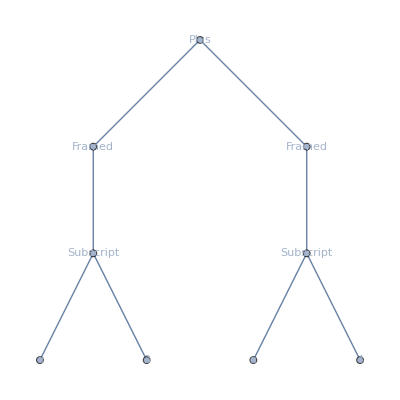
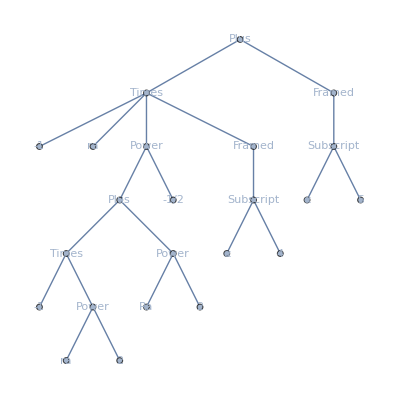
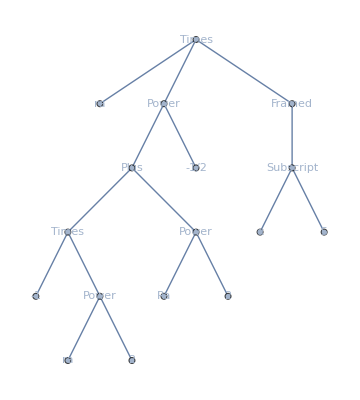
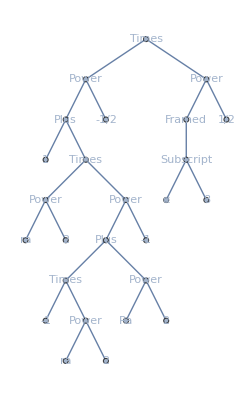
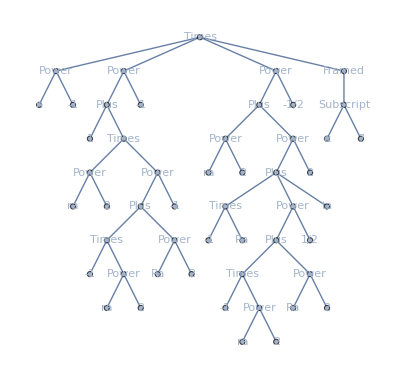
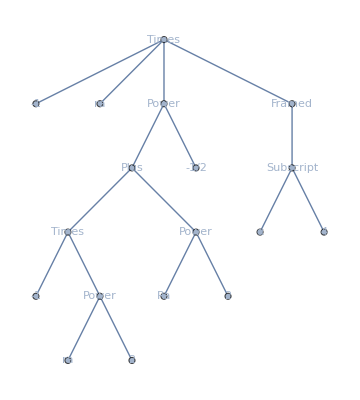
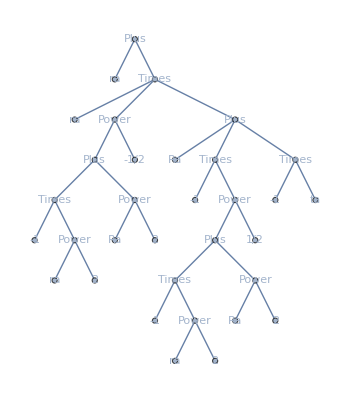
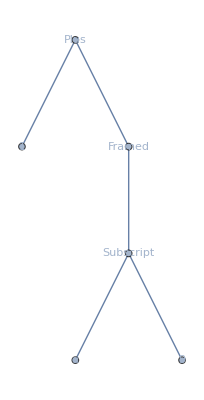
α_1→-Graphics-α_2→-Graphics-α_3→-Graphics-α_4→-Graphics-α_5→-Graphics-α_6→-Graphics-α_7→-Graphics-α_8→-Graphics-α_9→-Graphics-

```mathematica
MapAt[TreeFormToGraph,MapAt[TreeForm,subexpressionRules,{All,2}],{All,2}]//Row[#,Spacer[36]]&
```

Here we put the TreeFormToGraph of the replacedExpression

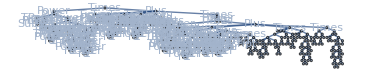

```mathematica
TreeFormToGraph[TreeForm[replacedExpression]]
```

Finally let’s compare our result to the TreeForm of expr1, which is messy

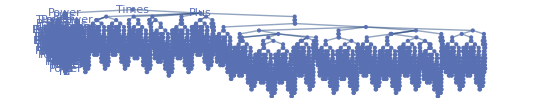

```mathematica
TreeFormToGraph[TreeForm[expr1]]
```